```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Deking, "Recuurent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 96, section 4.11*)
```

```mathematica
n0=5
```

5

```mathematica
(* substitution *)
```

```mathematica
s[1]={2,1,2,0,0,0,0,0,0}; s[2]={3,2,3,0,0,0,0,0,0}; s[3]={4,3,4,0,0,0,0,0,0};s[4]={5,4,5,0,0,0,0,0,0}; s[5]={1,5,1,0,0,0,0,0,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{1,2,0,0,0},{0,1,2,0,0},{0,0,1,2,0},{0,0,0,1,2},{2,0,0,0,1}}

```mathematica
MatrixForm[M]
```

(1 | 2 | 0 | 0 | 0
0 | 1 | 2 | 0 | 0
0 | 0 | 1 | 2 | 0
0 | 0 | 0 | 1 | 2
2 | 0 | 0 | 0 | 1)

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

33-5 x+10 x^2-10 x^3+5 x^4-x^5

```mathematica
(* solve Polynomial*)
```

```mathematica
NSolve[Det[M-x*IdentityMatrix[n0]]==0,x]
```

{{x→-0.618034-1.17557 ⅈ},{x→-0.618034+1.17557 ⅈ},{x→1.61803-1.90211 ⅈ},{x→1.61803+1.90211 ⅈ},{x→3.}}

```mathematica
Clear[s]
```

```mathematica
s[1]={2,1,2}; s[2]={3,2,3}; s[3]={4,3,4};s[4]={5,4,5}; s[5]={1,5,1};
```

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
w=Flatten[Table[s[i],{i,5}]]
```

{2,1,2,3,2,3,4,3,4,5,4,5,1,5,1}

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[2];
```

```mathematica
Length[aa]
```

135

```mathematica
(* second chord transform*)
```

```mathematica
(* pentatonic:BlackKeysPlusEAB{Db,Eb,Gb,Ab,Bb}*)
```

```mathematica
(*Cminor:https://www.pianoscales.org/pentatonic.html*)
```

```mathematica
v={9,6,3,1,11,9,6,3,1,11}
```

{9,6,3,1,11,9,6,3,1,11}

```mathematica
PiDigits=Table[v[[aa[[i]]]],{i,Length[aa]}]
```

{1,3,1,3,6,3,1,3,1,3,6,3,6,9,6,3,6,3,1,3,1,3,6,3,1,3,1,11,1,11,1,3,1,11,1,11,1,3,1,3,6,3,1,3,1,11,1,11,1,3,1,11,1,11,9,11,9,11,1,11,9,11,9,11,1,11,1,3,1,11,1,11,9,11,9,11,1,11,9,11,9,6,9,6,9,11,9,6,9,6,9,11,9,11,1,11,9,11,9,6,9,6,9,11,9,6,9,6,3,6,3,6,9,6,3,6,3,6,9,6,9,11,9,6,9,6,3,6,3,6,9,6,3,6,3}

```mathematica
SeedRandom[123]
```

RandomGeneratorState[…]

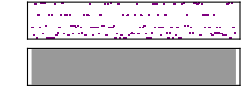

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_1.mid

```mathematica
snd1=Sound[Table[SoundNote[RandomChoice[{"HighWoodblock","Snare","Sticks","SideStick","BassDrum","MidTom","LowBongo","LowTom","LowWoodblock"}],.24],{i,Length[PiDigits]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_1.mid",snd1]
```

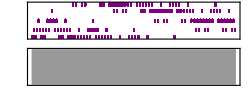

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_2.mid

```mathematica
snd2=Sound[Table[SoundNote[PiDigits[[i]],.24,"Piano"],{i,Length[PiDigits]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_2.mid",snd2]
```

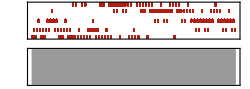

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_2a.mid

```mathematica
snd2a=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,"SynthBass2"],{i,Length[PiDigits]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_2a.mid",snd2a]
```

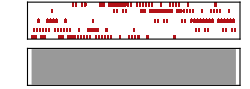

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_10.mid

```mathematica
(* 8th notes*)
snd10=Sound[Table[SoundNote[PiDigits[[i]]+24,.24,"Flute"],{i,Length[PiDigits]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_10.mid",snd10]
```

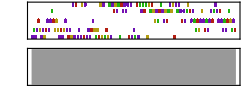

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_3.mid

```mathematica
snd3=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,RandomChoice[If[Mod[i,5]>0,{"Bass","ElectricBass","BassAndLead","PickedBass"},{"SynthBass2"}]]],{i,Length[PiDigits]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_3.mid",snd3]
```

```mathematica
w0={"Bass","ElectricBass","BassAndLead","PickedBass","SynthBass2"};
```

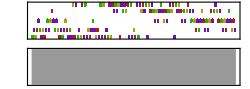

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_3a.mid

```mathematica
snd3a=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,w0[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_3a.mid",snd3a]
```

```mathematica
w1={"AltoSax","ElectricGuitar","Piano","Banjo","Whistle"};
```

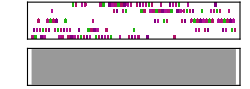

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_4a.mid

```mathematica
snd4a=Sound[Table[SoundNote[PiDigits[[i]],.24,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_4a.mid",snd4a]
```

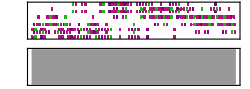

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_4b.mid

```mathematica
snd4b=Sound[Table[SoundNote[{PiDigits[[i]],PiDigits[[i]]+3},.24,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_4b.mid",snd4b]
```

```mathematica
snd5b=Sound[Table[SoundNote[{PiDigits[[i]],PiDigits[[i]]+3},.48,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_5b.mid",snd5b]
(* quarter notes*)
```

-Graphics-

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_5b.mid

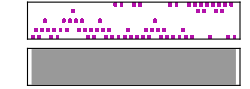

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_5.mid

```mathematica
snd5=Sound[Table[SoundNote[PiDigits[[i]]+24,.48,"Tinklebell"],{i,Floor[Length[PiDigits]/2]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_5.mid",snd5]
```

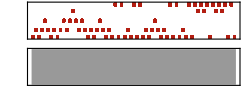

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_6.mid

```mathematica
snd6=Sound[Table[SoundNote[PiDigits[[i]]-24,0.48,"SynthBass2"],{i,Floor[Length[PiDigits]/2]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_6.mid",snd6]
```

```mathematica
snd13=Sound[Table[SoundNote[PiDigits[[i]]+12,.20,"Piano"],{i,Length[PiDigits]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_13.mid",snd13]
```

-Graphics-

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_13.mid

```mathematica
snd14=Sound[Table[SoundNote[PiDigits[[i]]-24,.20,"SynthBass2"],{i,Length[PiDigits]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_14.mid",snd14]
```

-Graphics-

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_14.mid

```mathematica
wa={0.96,0.24,0.24,0.24,0.24,0.96,0.24,0.24,0.48,0.96,0.12,0.12,0.12,0.12};
```

```mathematica
Apply[Plus,wa]
```

5.28

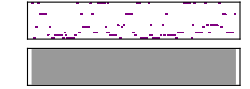

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_8.mid

```mathematica
snd8=Sound[Table[SoundNote[RandomChoice[{"Snare","Sticks","BassDrum","Claves","MidTom","LowBongo","LowTom"}],wa[[1+Mod[i,Length[wa]]]]],{i,Floor[Length[PiDigits]/2]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_8.mid",snd8]
```

```mathematica
wb={4*0.24,0.24,0.24,0.24,0.24,0.48,0.48,0.48,0.48,0.24,0.24,0.24,0.24,0.48,0.48};
```

```mathematica
Apply[Plus,wb]
```

5.76

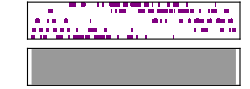

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_4c.mid

```mathematica
snd4c=Sound[Table[SoundNote[PiDigits[[i]],wa[[1+Mod[i,Length[wa]]]],"Piano"],{i,Ceiling[Length[PiDigits]]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_4c.mid",snd4c]
```

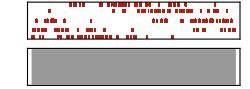

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_5c.mid

```mathematica
snd5c=Sound[Table[SoundNote[PiDigits[[i]]-12,wb[[1+Mod[i,Length[wb]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_5c.mid",snd5c]
```

```mathematica
Clear[wa,wb]
```

```mathematica
wa={0.12,0.12,0.12,0.12,0.24,0.24,0.48,0.48,0.24,0.24,0.24,0.24};
```

```mathematica
Apply[Plus,wa]
```

2.88

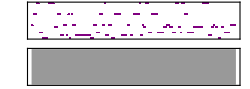

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2__9.mid

```mathematica
snd9=Sound[Table[SoundNote[RandomChoice[{"Snare","Sticks","BassDrum","Claves","MidTom","LowBongo","LowTom"}],wa[[1+Mod[i,Length[wa]]]]],{i,Floor[Length[PiDigits]/2]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2__9.mid",snd9]
```

```mathematica
wb={4*0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,3*0.24,0.12,0.12,0.12,0.12};
```

```mathematica
Apply[Plus,wb]
```

4.08

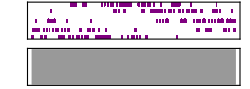

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_4d.mid

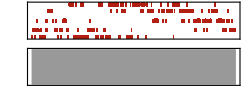

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_5d.mid

```mathematica
snd4d=Sound[Table[SoundNote[PiDigits[[i]],wa[[1+Mod[i,Length[wa]]]],"Piano"],{i,Ceiling[Length[PiDigits]]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_4d.mid",snd4d]
snd5d=Sound[Table[SoundNote[PiDigits[[i]]-12,wb[[1+Mod[i,Length[wb]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_5d.mid",snd5d]
```

```mathematica
wc={4*0.24,0.24,0.24,0.24,0.24,4*0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,2*0.48,4*0.24,0.24,0.24,0.24,0.24,4*0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,2*0.48};
```

```mathematica
Apply[Plus,wc]
```

13.44

```mathematica
w1={None,"Piano",None,"Piano",None,None,"Piano","Piano",None,None,"Piano","Piano",None,"Piano",None,"Piano",None,"Piano"};
```

```mathematica
snd4f=Sound[Table[SoundNote[{PiDigits[[i]]-5,PiDigits[[i]],PiDigits[[i]]+3},wc[[1+Mod[i,Length[wc]]]],w1[[1+Mod[i,8]]]],{i,Ceiling[Length[PiDigits]/3]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_4f.mid",snd4f]
```

Sound[{SoundNote[{-4,1,4},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{-4,1,4},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{1,6,9},0.96,None],SoundNote[{-2,3,6},0.24,Piano],SoundNote[{-4,1,4},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{-4,1,4},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{1,6,9},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{1,6,9},0.24,None],SoundNote[{4,9,12},0.24,Piano],SoundNote[{1,6,9},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{1,6,9},0.24,Piano],SoundNote[{-2,3,6},0.96,None],SoundNote[{-4,1,4},0.96,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{-4,1,4},0.24,None],SoundNote[{-2,3,6},0.24,Piano],SoundNote[{1,6,9},0.24,Piano],SoundNote[{-2,3,6},0.96,None],SoundNote[{-4,1,4},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{-4,1,4},0.24,Piano],SoundNote[{6,11,14},0.24,None],SoundNote[{-4,1,4},0.24,None],SoundNote[{6,11,14},0.24,Piano],SoundNote[{-4,1,4},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{-4,1,4},0.24,Piano],SoundNote[{6,11,14},0.24,None],SoundNote[{-4,1,4},0.24,Piano],SoundNote[{6,11,14},0.24,None],SoundNote[{-4,1,4},0.96,None],SoundNote[{-2,3,6},0.96,Piano],SoundNote[{-4,1,4},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{1,6,9},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{-4,1,4},0.96,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{-4,1,4},0.24,None]}]

SoundNote::invinst: "None" is not a valid style specification.

General::stop: Further output of SoundNote::invinst will be suppressed during this calculation.

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_4f.mid

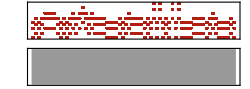

5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_5f.mid

```mathematica
snd5f=Sound[Table[SoundNote[{PiDigits[[i]]-5-12,PiDigits[[i]]-12,PiDigits[[i]]+3-12},wc[[1+Mod[i,Length[wc]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]/3]}]]
Export["5symbolSubstitution_Gosper_Border_Pentagon_BlackKeys_level2_5f.mid",snd5f]
```

```mathematica
(*end*)
```